```mathematica
(*Kerri McMahon          kmcmahon4@student.sjcny.edu
Nicholas Seaton      seatnk@farmingdale.edu*)

(*Question 1*)
```

```mathematica
Roots[z^7 - 5z^4+3z^2+6z-4 == 0,z]
```

z==Root0.589Root[-4+6 #1+3 #1^2-5 #1^4+#1^7&,1]0.5894209746196399||z==Root-0.903-0.782 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,2]-0.9034335945368862||z==Root-0.903+0.782 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,3]-0.9034335945368862||z==Root-0.667-1.55 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,4]-0.6668312565599425||z==Root-0.667+1.55 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,5]-0.6668312565599425||z==Root1.28-0.187 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,6]1.2755543637870086||z==Root1.28+0.187 ⅈRoot[-4+6 #1+3 #1^2-5 #1^4+#1^7&,7]1.2755543637870086

```mathematica
(*Question 2*)
```

```mathematica
ComplexPlot[z^7 - 5z^4+3z^2+6z-4 , {z, -2-2I, 2+2I}]
```

-Graphics-

```mathematica
(*Question 3*)
```

```mathematica
AbsArg[4-3I]
```

{5,-ArcTan[3/4]}

```mathematica
(*Question 4*)
```

```mathematica
Limit[Sqrt[9x^2 + 2]/(3-4x),x-> Infinity]
```

-3/4

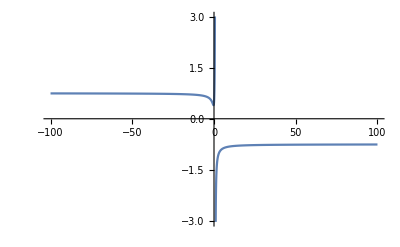

```mathematica
Plot[(√(9 x^2+2))/(3-4 x),{x,-100,100}]
```

```mathematica
(*Question 5*)
```

```mathematica
Limit[(1/x)Log[(x+2)/2],x-> 0]
```

1/2

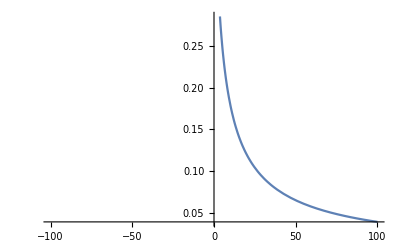

```mathematica
Plot[(1/x)Log[(x+2)/2], {x,-100,100}]
```

```mathematica
Question 6
```

6 Question

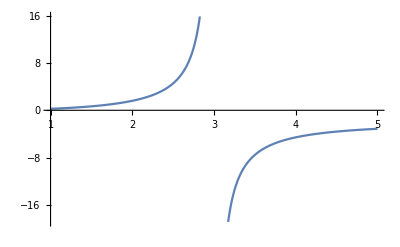

```mathematica
Plot[(2x^2)/(9-x^2),{x,1,5}]
```

```mathematica
Question 7
```

7 Question

```mathematica
Limit[(2x^2)/(9-x^2), x-> 3]
```

Indeterminate

8 Question

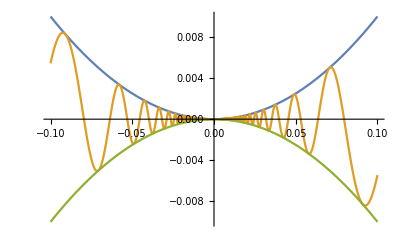

```mathematica
Question 8

Plot[{x^2,x^2Sin[1/x], -x^2}, {x,-.1,.1}]
```

```mathematica
Question 9
```

9 Question

```mathematica
Limit[x^2Sin[1/x],x->0]
```

0

```mathematica
(* As shown in the plot above the sine function continues to infinitely oscillate. As the function approaches 0 from both sides of the x-axis the funcion eventually hits (0,0).*)
```

10 Question

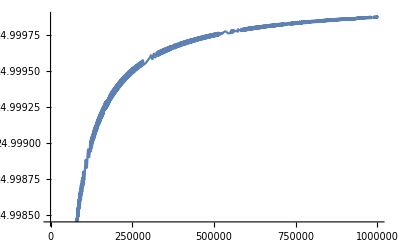

```mathematica
Question 10

Plot [(x - Sqrt[Sin[x]+10x+x^2])^2, {x,0,1000000}]
```

```mathematica
Question 11
```

11 Question

```mathematica
Limit[(x - Sqrt[Sin[x]+10x+x^2])^2,x->Infinity]
```

25

```mathematica
Question 12
```

12 Question

```mathematica
f[x_]:=.99x^3-21x^2+120x-100
g[x_]:=1.00x^3-21x^2+120x-100
h[x_]:=1.01x^3-21x^2+120x-100
```

```mathematica
Roots[f[x]==0,x]
```

x==1.00012||x==9.0413||x==11.1707

```mathematica
Roots[g[x]==0,x]
```

x==1.||x==10.||x==10.

```mathematica
Roots[h[x]==0,x]
```

x==0.999877||x==9.8961-1.0437 ⅈ||x==9.8961+1.0437 ⅈ

```mathematica
Question 13
```

13 Question

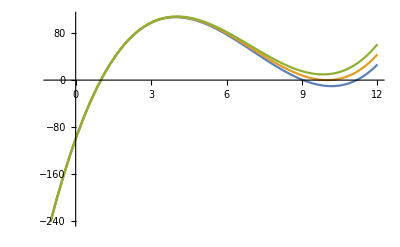

```mathematica
Plot[{f[x],g[x],h[x]}, {x,-1,12}]
```

```mathematica
(*Question 14*)
system1 = {x - y == 3,4x^2 + y^2 ==4}
Solve[system1, {x,y}, Complexes]
```

{x-Cos[t]==3,4 x^2+Cos[t]^2==4}

{{x→3/5-(4 ⅈ)/5,Cos[t]→-12/5-(4 ⅈ)/5},{x→3/5+(4 ⅈ)/5,Cos[t]→-12/5+(4 ⅈ)/5}}

```mathematica
(*Question 15*)
```

```mathematica
system1 = {4 x^2+y^2==4,x-y==3}
ContourPlot[system1,{x,-3,3},{y,-3,3}]
```

{4 x^2+Cos[t]^2==4,x-Cos[t]==3}

-Graphics-

```mathematica
(*The need for complex solutions becomes apparent 
here since according to the real domain above,
this system of equations has NO solution. However,
we know,as per our above calculations, that solutions exist 
in the complex domain.*)

(*Question 16*)

 FunctionPeriod[(15* Sin[12x]^2) + (12*Sin[15x]^2),x]
```

π/3

```mathematica
(* Question 17*)
```

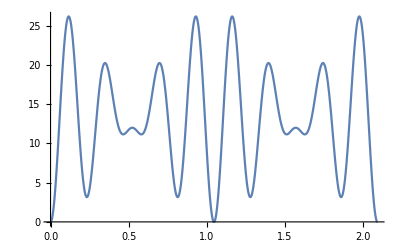

```mathematica
Plot[(15* Sin[12x]^2) + (12*Sin[15x]^2), {x,0,2π/3}]
```

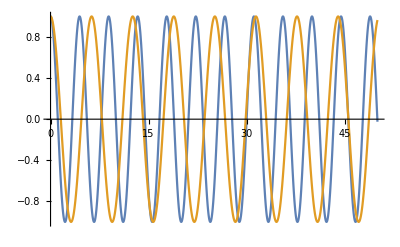

```mathematica
(*Question 18*)
Plot[ {y= Cos[t*(2^(1/2))] ,y = Cos[t]},{t,0,50}]
```

```mathematica
(*Period of first term*)
FunctionPeriod[y= Cos[t*(2^(1/2))] ,t]
```

√2 π

```mathematica
√2 π
(*Period of second term*)
FunctionPeriod[y = Cos[t],t]
```

√2 π

2 π

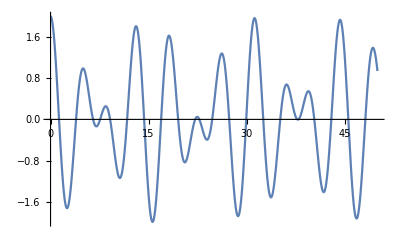

```mathematica
(*Superposition*)
Plot[ {(y= Cos[t*(2^(1/2))]) +(y = Cos[t])},{t,0,50}]
```

```mathematica
(*Period of the superposition*)
FunctionPeriod[(y= Cos[t*(2^(1/2))]) +(y = Cos[t]),t]
```

0

```mathematica
(* The superposition of two waves is the sum of the two waves together. 
Initially, we used the FunctionPeriod[] function to mathematically prove
the two waves initally were periodic, and we took the period of the
superposition of the two waves, and it was evaluated to be zero.
We can also notice that visually, the superposition has no
noticable periodic patterns and further demnstrates that
the superposition of two initially periodic waves can
be periodic.  *)


(*Question 19*)
f[x_] = Log[1-5x^2 + x^3]
f'[x]
```

Log[1-5 x^2+x^3]

(-10 x+3 x^2)/(1-5 x^2+x^3)

```mathematica
Log[1-5 x^2+x^3]
```

Log[1-5 x^2+x^3]

```mathematica
(*Question 20*)
f[x_] := ((3x)(5x^2))
f'[x]
```

45 x^2

```mathematica
(*Question 21*)
f[x_] = ((1 + ⅇ^(-2x))/(x + Tan[12x]))
(*Derivative of term*)
 eval = f'[x]
(*Further simplification?*)
Simplify[eval]
```

(1+ⅇ^(-2 x))/(x+Tan[12 x])

-((1+ⅇ^(-2 x)) (1+12 Sec[12 x]^2))/(x+Tan[12 x])^2-(2 ⅇ^(-2 x))/(x+Tan[12 x])

-((1+ⅇ^(-2 x)) (1+12 Sec[12 x]^2)+2 ⅇ^(-2 x) (x+Tan[12 x]))/(x+Tan[12 x])^2

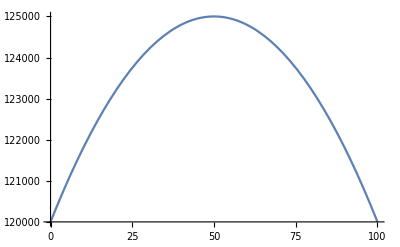

```mathematica
(*Question 22*)
(*Optimal selling price: $250 - 50 represents the amount decremented from original price, 300
Gross monthly sales: 125,000*)

(* y = units sold
x = price in USD*)
Plot[(400 + 2x)(300 - x), {x,0,100}]
```

```mathematica
(*Question 23*) 

Integrate[Csc[x]Cot[x],x]
```

-Csc[x]

```mathematica
(*Question 24*)
Integrate[2Sin[x]Cos[x],x]
```

-1/2 Cos[2 x]

ⅇ^Sin[x]

Sin[Sin[x]]

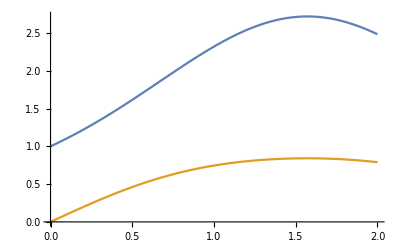

```mathematica
(*Question 25*)
(*Initial assignment variables and plotting*)
f[x_] := ⅇ^Sin[x]
g[x_] := Sin[Sin[x]]

ff = f[x]
gg = g[x]
Plot[{ff,gg},{x,0,2}]
```

```mathematica
(*Area between the curves
1. Calculate big area then small area via definite integrals
2. Subtract
*)
f[x_] := Sin[Sin[x]]
g[x_] := ⅇ^Sin[x]

NIntegrate[g[x]-f[x],{x,0,2}]
```

2.98948

```mathematica
(*Question 26*)

(*Using Plot3D*)

Plot3D[z = Abs[Sqrt[x]],{x,-1,1},{y,-1,1}, RegionFunction-> Function[{x,y,z},0<x^2 + y^2 < 1]]
```

-Graphics3D-

```mathematica
(* Question 27*)

(* Volume under the 
surface Double integral of the top surface, our graph, 
minus the bottom surface, z=0*)

Integrate[Abs[Sqrt[x]],{x,0,1},{y,0,1}]
```

2/3

```mathematica
(*Question 28*)
ff =( x^2 + y^2 +1);
Integrate[ff,{x,0,(2-2x)},{y,0,1}]
```

4/3 (2-2 x)+1/3 (2-2 x)^3

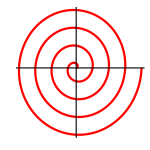

```mathematica
(*Question 29*)
ParametricPlot[t{Cos[t],Sin[t]},{t,0,8Pi},Ticks->None,PlotStyle->Red,ImageSize->150]
```

```mathematica
spiral= t{Cos[t],Sin[t]};
FullSimplify[ArcLength[spiral,{t,0,8Pi}]]
```

1/2 (8 π √(1+64 π^2)+ArcSinh[8 π])

```mathematica
(* Question 30 - Let's start by defining points. Let's say the rightmost bottom corner is (0,0) our origin.
Moving to the left, the point where the ladder hits the wall we will say has a distance of a. 
Next we will say the point above the origin where the ladder hits the wall is b. b can be defined as 
Sqrt(L^2 - a^2) using the Pythagorean Theorem. The ladder in conjuction with the walls create a right triangle which is why we ca use this theorem. Now we can define the line the ladder creates as follows *)
```

```mathematica
y[x_]:=(Sqrt[L^2 - a^2]/a)x +Sqrt[L^2 - a^2]
```

```mathematica
y[x]
```

```mathematica
√(-a^2+L^2)+(√(-a^2+L^2) x)/a
(*We must set this equation to 0 in order to get a desired outcome*)
```

```mathematica
g[x_]:=(Sqrt[L^2 - a^2]/a)x +Sqrt[L^2 - a^2] - y
```

```mathematica
g[x]
```

√(-a^2+L^2)+(√(-a^2+L^2) x)/a-y

```mathematica
(*Next we can say that when the ladder touches the innermost corner the ladder will be stuck. This point is 
(1m,2m) This means that the line the ladder creates must obey the following inequality.*)
```

```mathematica
Θ[a_]:= √(-a^2+L^2)+(√(-a^2+L^2) m)/a-2m
```

```mathematica
Θ[a]
```

√(-a^2+L^2)-2 m+(√(-a^2+L^2) m)/a

```mathematica
(*From here we can see that when Θ[a] => 0, for all 0<a<L, the latter can be rotated without getting stuck.
Now to solve for the maximum L we have to get the second derivative which wll tell us if the critical value
is a minimum or maximum*)
```

```mathematica
d[Θ[a]]:=D[Θ[a],a]
```

```mathematica
FullSimplify[D[Θ[a],a]]
```

-(a^3+L^2 m)/(a^2 √(-a^2+L^2))

```mathematica
r[d_]:=D[d[Θ[a]],a]
```

```mathematica
FullSimplify[D[d[Θ[a]],a]]
```

-(L^2 (a^3+3 a^2 m-2 L^2 m))/(a^3 (-a^2+L^2)^(3/2))

```mathematica
(*Because the second derivative is concave up the critical value is a minimum. So we fill take the first derivative
and solve for a. Then we plug this in back to our original equation and this will yeild us our L max.*)
```

```mathematica
Solve[d[Θ[a]]==0,a]
```

{{a→-L^(2/3) m^(1/3)},{a→(-1)^(1/3) L^(2/3) m^(1/3)},{a→-(-1)^(2/3) L^(2/3) m^(1/3)}}

```mathematica
a1:=-L^(2/3) m^(1/3)
Θ[a1]
```

√(L^2-L^(4/3) m^(2/3))-(√(L^2-L^(4/3) m^(2/3)) m^(2/3))/L^(2/3)-2 m

```mathematica
Solve[Θ[a1]==0,L]
```

{{L→-√(5 m^2+6 2^(1/3) m^2+3 2^(2/3) m^2)},{L→√(5 m^2+6 2^(1/3) m^2+3 2^(2/3) m^2)},{L→-√(5 m^2-(3 m^2)/2^(1/3)-3 2^(1/3) m^2+(3 ⅈ √3 m^2)/2^(1/3)-3 ⅈ 2^(1/3) √3 m^2)},{L→√(5 m^2-(3 m^2)/2^(1/3)-3 2^(1/3) m^2+(3 ⅈ √3 m^2)/2^(1/3)-3 ⅈ 2^(1/3) √3 m^2)},{L→-√(5 m^2-(3 m^2)/2^(1/3)-3 2^(1/3) m^2-(3 ⅈ √3 m^2)/2^(1/3)+3 ⅈ 2^(1/3) √3 m^2)},{L→√(5 m^2-(3 m^2)/2^(1/3)-3 2^(1/3) m^2-(3 ⅈ √3 m^2)/2^(1/3)+3 ⅈ 2^(1/3) √3 m^2)}}

```mathematica
(*From the above the only non-negative real answer is below*)
```

```mathematica
Lmax:=√(5 m^2+6 2^(1/3) m^2+3 2^(2/3) m^2)
```

```mathematica
(*Question 31*)
```

```mathematica
FullSimplify[x^3y^2-3x^2y-2xy^3+6y^2]
```

-2 xy^3+y (-3 x^2+(6+x^3) y)

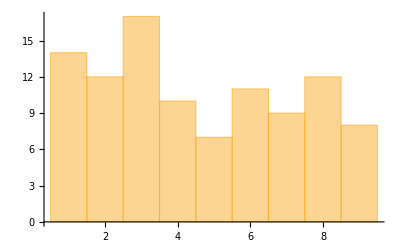

{1/3,1/3,1/3,1,1/8,1/6,1/2,1/2,1/8,1/7,1/7,1,1/4,1/7,1,1,1/2,1/9,1/2,1/6,1/5,1/7,1/7,1/3,1/7,1/9,1/9,1/6,1/5,1/2,1/2,1,1,1/7,1/8,1/3,1/5,1/9,1/2,1/4,1/2,1,1/8,1/5,1/5,1/2,1/6,1/8,1/3,1/3,1,1/3,1/6,1/3,1/6,1/8,1/2,1/8,1/7,1/4,1/3,1/3,1,1,1/2,1/4,1/3,1/3,1/3,1/4,1/6,1/3,1/8,1/6,1/6,1,1/4,1/9,1,1/9,1/5,1/8,1/5,1/4,1/6,1/4,1/8,1/4,1/3,1,1/6,1/2,1/4,1/8,1/9,1/7,1/3,1/9,1,1/8}

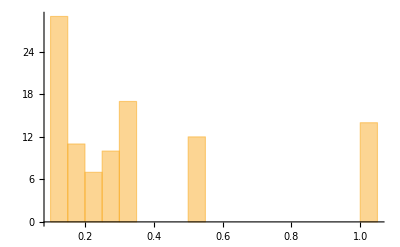

```mathematica
(*Question 32*)

random=RandomReal[{1,100},100];
(*Table[First[RealDigits[random,2,1]],{x,0,100}]*)
ints := IntegerPart[random] (* just cleaning the data*)
(* list := RealDigits[random]*)
 ourdigits := RealDigits[ints]
finallist:= ourdigits[[All,1]]
firstdigits := finallist[[All,1]](* list of first digits in our set!!!*)
(* Now we have this set, count the occurence of digits 0-9.*)

Histogram[{firstdigits},{1}](* first graph - frequencies of each first digit value in set*)
inverse = 1/ firstdigits;
inverse
Histogram[{inverse},{.05}](* second graph - frequencies of reciprocals*)

(* Reciprocal value 1/8 occured the most frequently!*)
```

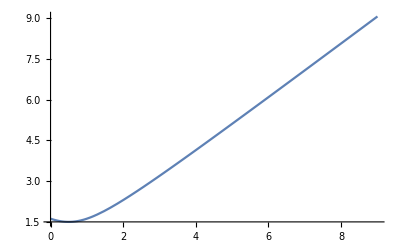

1/(1/2 (1+√5)+1/(1/2 (1+√5)+1/(1/2 (1+√13)+1/(1/2 (1+√29)+1/(1/2 (1+√53)+1/(1/2 (1+√85)+1/(1/2 (1+5 √5)+1/(1/2 (1+√173)+1/(1/2 (1+√229)+2/(1+√293))))))))))

13-12 #1+4 #1^2&

```mathematica
(*Question 33*)

f[x_] := (1 + Sqrt[4x^2-4x+5])/2;
Plot[f[x],{x,0,9}]
ContinuedFractionK[f[x], {x,0,9}]
FromContinuedFraction[{.5(1 + Sqrt[5]), .5(1 + Sqrt[5]), .5(1 + Sqrt[13]), .5(1 + Sqrt[29]), .5(1 + Sqrt[53]),
 .5(1 + Sqrt[85]), .5(1 + Sqrt[125]), .5(1 + Sqrt[173]), .5(1 + Sqrt[229]), .5(1 + Sqrt[293])}];
 k := ContinuedFraction[2.11718];
FindSequenceFunction[{5,5,13,29,53,85,125,173,229,293}]
```

```mathematica
(*^^^^ The pattern in the numbers under the radical in each term^^^*)
```

```mathematica
(*Question 34*)
 num:= PrimePi[300](* finding amount of primes between 0 and 300*)
t :=Table[Prime[n],{n,num}] (* creating a table of prime numbers from 0 to 62*)
newt :=Differences[t](* new table of differences*)
maxpos := Ordering[newt,-1](*max difference occurs at this position*)
Part[t,maxpos]
Part[t, maxpos +1]
```

{113}

{127}

```mathematica
(*Question 35*)
```

```mathematica
Solve[{a +b-2c+d+3e-f==4,2a-b+c+2d+e-3f==20,a+3b-3c-d+2e+f==-15,
5a+2b-c-d+2e+f==-3,-3a-b+2c+3d+e+3f==16,4a+3b+c-6d-3e-2f==-27},
{a,b,c,d,e,f}]
```

{{a→1,b→-2,c→3,d→4,e→2,f→-1}}